```mathematica
Clear[pdfactive]
```

```mathematica
pdfactive[Nnuclei_, pactive_, Nactive_] = Simplify[PDF[BinomialDistribution[Nnuclei,pactive],Nactive],{ 0<=Nactive≤ Nnuclei}]
```

(1-pactive)^(-Nactive+Nnuclei) pactive^Nactive Binomial[Nnuclei,Nactive]

```mathematica
pdfdetect[ntrials_, pdetect_, nany_] = Simplify[PDF[BinomialDistribution[ntrials,pdetect],nany], {0≤nany≤ntrials}]
```

(1-pdetect)^(-nany+ntrials) pdetect^nany Binomial[ntrials,nany]

```mathematica
logL[Nnuclei_, pactive_, ntrials_, pdetect_, Nactive_, nany_] = FullSimplify[Log[pdfdetect[ntrials, pdetect]*pdfactive[Nnuclei, pactive]]]
```

Log[(1-pactive)^(-Nactive+Nnuclei) pactive^Nactive (1-pdetect)^(-Nany+ntrials) pdetect^Nany Binomial[Nnuclei,Nactive] Binomial[ntrials,Nany]]

```mathematica
f[Nany_, pdetect_] = FullSimplify[D[logL[20, pactive,2, pdetect, 16, 12], pdetect]]
```

(Nany-2 pdetect)/(pdetect-pdetect^2)

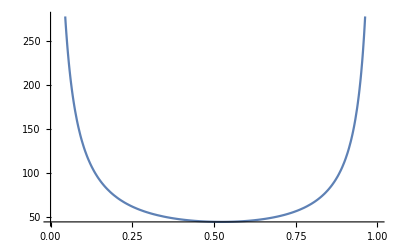

```mathematica
Plot[(Nany-2 pdetect)/(pdetect-pdetect^2) /.Nany->12,{pdetect,0,1}]
```

```mathematica
ArgMax[(Nany-2 pdetect)/(pdetect-pdetect^2) /. Nany->1000, pdetect]
```

0

```mathematica
f[6, .5]
```

(Nany-2 pdetect)/(pdetect-pdetect^2)[6,0.5]

```mathematica
Plot[f[6, pdetect], {pdetect, 0, 1}]
```

-Graphics-

```mathematica
pdetecthat = FullSimplify[ArgMax[D[logL[20, pactive,2, pdetect, 16, 12], pdetect], pdetect], {ntrials>0, Nany>0}]
```

FullSimplify::infd: Expression ArgMax[((1-pdetect)^(-2+Nany) pdetect^-Nany (4845 Nany (1-pactive)^4 pactive^16 (1-pdetect)^(2-Nany) pdetect^(-1+Nany) Binomial[2,Nany]-4845 (2-Nany) (1-pactive)^4 pactive^16 (1-pdetect)^(1-Nany) pdetect^Nany Binomial[2,Nany]))/(4845 (1-pactive)^4 pactive^16 Binomial[2,Nany]),pdetect] simplified to Indeterminate.

Indeterminate

```mathematica
pactivehat = FullSimplify[D[logL[Nnuclei, pactive,ntrials, pdetect], pactive]]
```

(Nactive-Nnuclei pactive)/(pactive-pactive^2)

```mathematica
Δt =
```

```mathematica
npols[r_, Δt_] =PDF[PoissonDistribution[r*Δt], k]
```

Piecewise[{{(ⅇ^(-r Δt) (r Δt)^k)/(k!), k≥0}, {0, True}}]

```mathematica
𝒫=CompoundPoissonProcess[.8,PoissonDistribution[2]]
```

CompoundPoissonProcess[0.8,PoissonDistribution[2]]

```mathematica
data=RandomFunction[𝒫,{8}]
```

TemporalData[…]

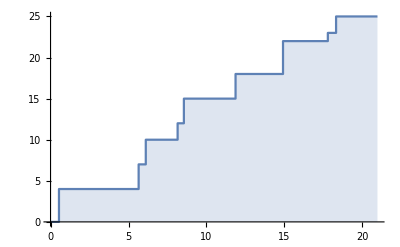

```mathematica
ListStepPlot[data,Filling->Axis]
```

```mathematica
data=RandomVariate[SliceDistribution[𝒫,8],10^5];
```

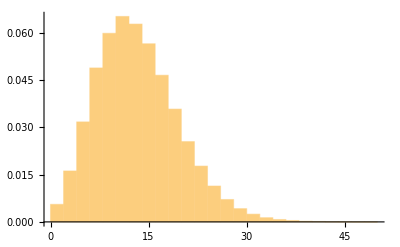

```mathematica
Histogram[data,20,"PDF"]
```

```mathematica
WeakStationarity[𝒫]
```

False

```mathematica
pngivent[n_,r_,t_] =Simplify[PDF[PoissonDistribution[r*t], n], n>0]
```

(ⅇ^(-r t) (r t)^n)/(n!)

```mathematica
Clear[pngivent]
```

```mathematica
pngivent[n_,r_,t_]  = (ⅇ^(-r t) (r t)^n)/(n!)
```

(ⅇ^(-r t) (r t)^n)/(n!)

```mathematica
pt[j_,t_] = Simplify[PDF[ExponentialDistribution[j],t],t≥0]
```

ⅇ^(-j t) j

```mathematica
Clear[pt]
```

```mathematica
pt[j_,t_] = ⅇ^(-j t) j
```

ⅇ^(-j t) j

```mathematica
pn[j_,r_, n_] = Simplify[Integrate[pngivent[n,r,t]*pt[j,t],{t,0,∞}], {n>0, r>0, j>0, n∈Integers}]
```

(j r^n (j+r)^(-1-n) Gamma[1+n])/(n!)

```mathematica
pn[j_,r_, n_] = j r^n (j+r)^(-1-n)
```

j r^n (j+r)^(-1-n)

```mathematica
Sum[pn[j, r, n], {n, 0, ∞}]
```

1

```mathematica
Manipulate[DiscretePlot[j r^n (j+r)^(-1-n),{n,0,10}, PlotRange->{{0,10},{0,1}}],{j,.1,20},{r,.1,20}]
```

```mathematica
𝒟=ProbabilityDistribution[pn[j,r],{j,0,Infinity}, {r,0,Infinity}];
```

```mathematica
ProbabilityDistribution[((x1 x2^n (x1+x2)^(-1-n) Gamma[1+n])/(n!))[x1,x2],{x1,0,∞},{x2,0,∞}]
```

ProbabilityDistribution[(x1 x2^n (x1+x2)^(-1-n) Gamma[1+n])/(n!)[x1,x2],{x1,0,∞},{x2,0,∞}]

```mathematica
Integrate[Simplify[PDF[𝒟,{j,r}],{j,0,∞},{r,0,∞}, {j>0, r>0}], {j,0,∞},{r,0,∞}]
```

Simplify::nonopt: Options expected (instead of {j>0,r>0}) beyond position 2 in Simplify[Piecewise[{{(j r^n (j+r)^(-1+Times[«2»]) Gamma[1+n])/(n!), j>0&&r>0}, {0, True}}],{j,0,∞},{r,0,∞},{j>0,r>0}]. An option must be a rule or a list of rules.

```mathematica
Solve[1-(NAUB/Nact) == (1- (No - Nact))^n, Nact]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1-NAUB/Nact==(1+Nact-No)^n,Nact]

```mathematica
eq = 1-(NAUB/Nact) == (1- (No - Nact))^n
```

1-NAUB/Nact==(1+Nact-No)^n

```mathematica
x = Solve[1-(NAUB/Nact) == (1- (No - Nact))^n, Nact]
```

```mathematica
x=Nact/.Solve[eq&&Nact>0,Nact]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

ReplaceAll::reps: {Solve[1-NAUB/Nact==(1+Nact-No)^n&&Nact>0,Nact]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Nact/.Solve[1-NAUB/Nact==(1+Nact-No)^n&&Nact>0,Nact]

```mathematica
Expectation[GammaDistribution[1, 1/p], p]
```

```mathematica
Clear[n]
```

```mathematica
Simplify[Expectation[τ\[Conditioned]τ<T,τ\[Distributed] GammaDistribution[n,1/p]], {T>0, n∈Integers}]
%//TeXForm
```

(Gamma[1+n]-Gamma[1+n,p T])/(p Gamma[n]-p Gamma[n,p T])

\frac{\Gamma (n+1)-\Gamma (n+1,p T)}{p \Gamma (n)-p \Gamma (n,p T)}

```mathematica
Simplify[Piecewise[{{(Gamma[1+N]-Gamma[1+N,p T])/(p (Gamma[N]-Gamma[N,p T])),T>0}},0]]
```

Piecewise[{{(Gamma[1+N]-Gamma[1+N,p T])/(p Gamma[N]-p Gamma[N,p T]), T>0}, {0, True}}]

```mathematica
Probability[tauGammaDistribution[1, 1/p], p]
```

```mathematica
dphidr = {Cos[θ], Sin[θ], -r/Sqrt[1-r^2]};
dphidtheta = {-r*Sin[θ], r*Cos[θ], 0};
cr = Cross[dphidr, dphidtheta]
Norm[cr]
```

{(r^2 Cos[θ])/(√(1-r^2)),(r^2 Sin[θ])/(√(1-r^2)),r Cos[θ]^2+r Sin[θ]^2}

√(Abs[(r^2 Cos[θ])/(√(1-r^2))]^2+Abs[(r^2 Sin[θ])/(√(1-r^2))]^2+Abs[r Cos[θ]^2+r Sin[θ]^2]^2)